```mathematica
(*       Near-Helmholtz Field Configuration        *)
```

{(ρ Cos[Theta] Cos[θ])/((1+ρ^2-2 ρ Cos[Theta] Sin[θ])^(3/2)),(ρ Cos[θ] Sin[Theta])/((1+ρ^2-2 ρ Cos[Theta] Sin[θ])^(3/2)),(1-ρ Cos[Theta] Sin[θ])/((1+ρ^2-2 ρ Cos[Theta] Sin[θ])^(3/2))}

(2 Cot[θ] ((1+ρ^2) EllipticE[(4 ρ Sin[θ])/(1+ρ^2+2 ρ Sin[θ])]-EllipticK[(4 ρ Sin[θ])/(1+ρ^2+2 ρ Sin[θ])] (1+ρ^2-2 ρ Sin[θ])))/((1+ρ^2-2 ρ Sin[θ]) √(1+ρ^2+2 ρ Sin[θ]))

(2 (-(-1+ρ^2) EllipticE[(4 ρ Sin[θ])/(1+ρ^2+2 ρ Sin[θ])]+EllipticK[(4 ρ Sin[θ])/(1+ρ^2+2 ρ Sin[θ])] (1+ρ^2-2 ρ Sin[θ])))/((1+ρ^2-2 ρ Sin[θ]) √(1+ρ^2+2 ρ Sin[θ]))

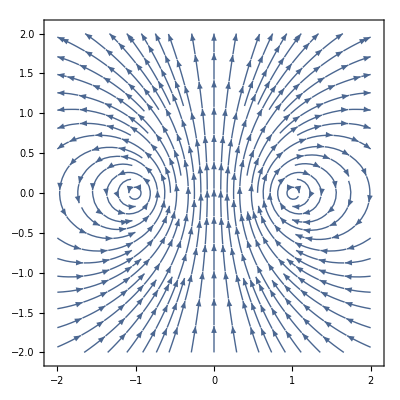

```mathematica
s=1;
m=4*Pi*10^7;
l[Theta_]:={s Cos[Theta],s Sin[Theta],0};
R={x,y,z}-l[Theta];
r=R/Sqrt[R.R];
Deel=D[l[Theta],Theta];
Cross[Deel,r];
Integrand=%/R.R;
int2=Simplify[Integrand/.Thread[{x,y,z}->ρ {Cos[ϕ] Sin[θ],Sin[ϕ] Sin[θ],Cos[θ]}/.ϕ->0],ρ>0&&θ>0&&ϕ>0&&Theta>0]
Bx=2 Assuming[ρ>0&&Pi/2>θ>0,Integrate[int2[[1]],{Theta,0,Pi}]]
Bz=2 Assuming[ρ>0&&Pi/2>θ>0,Integrate[int2[[3]],{Theta,0,Pi}]]
StreamPlot[{Bx,Bz}/.{θ->ArcTan[z,x],ρ->Sqrt[x^2+z^2]},{x,-2,2},{z,-2,2}]
```